# HyperBloch package tutorial

## Flat-bands; hyperbolic Lieb lattices

This notebook provides solved exercises aimed to introduce the functionality of the  HyperBloch package for efficient modeling of tight-binding models on hyperbolic lattices. It is intended to be used in tandem with the HyperBloch Flat-bands tutorial on the HyperCells&HyperBloch website. In this tutorial we demonstrate the emergence of flat-bands in the density of states of an elementary nearest-neighbor hopping model on the {6,4}-Lieb lattice. In particular, we emphasize the workflow for Abelian Hyperbolic band theory (AHBT) analysis with the supercell method of Lieb (supercell) model graphs  (constructed through HyperBloch’s sister package HyperCells), which is structurally unchanged compared to the analysis of tessellation (supercell) model graphs.

## Preliminaries:

### Remarks:

Before using the notebook to the Flat-bands tutorial for hyperbolic Lieb lattices:

Make sure that the HyperBloch package is installed, if this is not the case please follow the instruction on the website HyperCells&HyperBloch installation.

Make sure that the required files .hcc,  .hcm and .hcs files are in the current directory. This entails files:

(2,4,6)_T2.2_3.hcc
{6,4}-Lieb_T2.2_3.hcm
{6,4}-Lieb_T2.2_3_sc-T5.4.hcs
{6,4}-Lieb_T2.2_3_sc-T9.3.hcs

In case no such files exist in your current directory, please follow the instructions in the  HyperBloch Flat-bands tutorial,  or download the files there.

### Documentation:

You may want to take a look at the basic usage guide of the HyperBloch package or the available functions within the package, respectively:

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/tutorial/BasicUsage"];
```

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/guide/HyperBlochPackage"];
```

### Load the HyperBloch package:

The HyperBloch package can be loaded as follows:

```mathematica
<<PatrickMLenggenhager`HyperBloch`
```

Set the directory of the needed HyperCells files remarked above, which is assumed to be the directory of this file:

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Needed functions:

In previous tutorials, getting started with the HyperBloch package and HyperBloch Supercells tutorial, we have calculated the density of states of various nearest-neighbor tight-binding models via exact diagonalization and random samples. We predefine a function in order to calculate the eigenvalues for the Abelian Bloch Hamiltonians that we will construct. We  take advantage of the independence of different momentum sectors and parallelize the computation, where we partition the set of Npts into  Nruns subsets:

```mathematica
ComputeEigenvalues[cfH_,Npts_,Nruns_,genus_]:=
Flatten@ParallelTable[
Flatten@Table[
Eigenvalues[cfH@@RandomReal[{-Pi,Pi},2genus]],{i,1,Round[Npts/Nruns]}],
{j,1,Nruns},Method->"FinestGrained"]
```

## {6,4} Lieb lattice:

### Preliminaries:

We consider the following sequence of supercells, defined in terms of triangle group quotients given in the tabulated list of quotients by Marston Conder:

```mathematica
cellsLieb={"T2.2","T5.4","T9.3"};
```

where we consider the unit cell T2.2 as the primitive cell.

### Import (supercell) model graphs:

We first import the cell, model, and supercell model graphs as produced by the HyperCells package:

Cell graph:

```mathematica
pcellLieb=ImportCellGraphString[Import["(2,4,6)_T2.2_3.hcc"]];
```

Primitive cell:

```mathematica
pcmodelLieb=ImportModelGraphString[Import["{6,4}-Lieb_T2.2_3.hcm"]];
```

Consecutive supercells:

```mathematica
scmodelsLieb=Association[#->ImportSupercellModelGraphString[ Import["{6,4}-Lieb_T2.2_3_sc-"<>#<>".hcs"]]&/@cellsLieb[[2;;]]];
```

We can extract the genera of the compactified unit cells programmatically:

```mathematica
genusLstLieb = Join[
Association[cellsLieb[[1]]->pcmodelLieb["Genus"]],
Association[#->scmodelsLieb[#]["Genus"]&/@cellsLieb[[2;;]]]
];
```

### Visualize the model graph:

We can visualize the model graph with the high-level visualization function VisualizeModelGraph:

```mathematica
VisualizeModelGraph[pcmodelLieb,
CellGraph->pcellLieb,
NumberOfGenerations->3,
Elements-><|
	ShowCellGraphFlattened->{},
	ShowCellBoundary->{ShowEdgeIdentification->True}
|>,
ImageSize->400]
```

-Graphics-

### Construct Abelian Bloch Hamiltonians:

Once the (supercell) model graphs are imported the corresponding Abelian Bloch Hamiltonians can be constructed.

Primitive cell:

```mathematica
HpcLieb=AbelianBlochHamiltonian[pcmodelLieb,1,0&,-1&,CompileFunction->True];
```

Consecutive supercells (this might take a minute):

```mathematica
HscLieblst=Association[#->AbelianBlochHamiltonian[scmodelsLieb[#],1,0&,-1&,PCModel->pcmodelLieb,CompileFunction->True]&/@cellsLieb[[2;;]]];
```

For convenience, let us collect the constructed Hamiltonians in one Association:

```mathematica
HcLieblst=Join[Association[cellsLieb[[1]]->HpcLieb],HscLieblst];
```

### Density of states:

We compute the Eigenvalues with a set of  10^4 random samples in momentum space and 32 subsets, (this might take a minute):

```mathematica
evalsLieb=Association[#->ComputeEigenvalues[HcLieblst[#],10^4,32,genusLstLieb[#]]&/@cellsLieb];
```

Let us construct a list of colors for the different unit cells we are considering:

```mathematica
cLst=(ColorData["SunsetColors","ColorFunction"]/@(1-Range[1,3]/3.));
```

We choose to visualize the density of states via a kernel density estimation with an energy binwidth of 0.01, (this might take a minute):

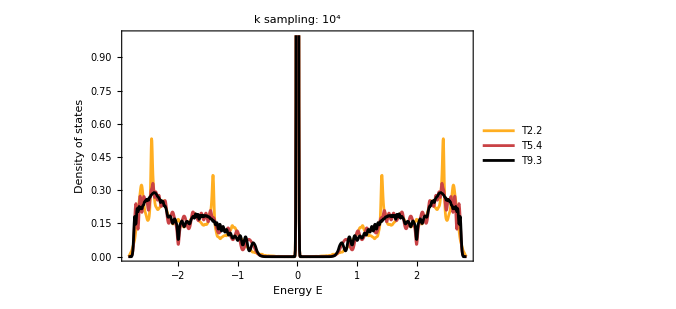

```mathematica
SmoothHistogram[evalsLieb,0.01,"PDF",
Frame->True,FrameLabel->{"Energy E","Density of states"},FrameStyle->Black,
ImageSize->500,ImagePadding->{{Automatic, 10}, {Automatic, 10}},LabelStyle->20,
PlotLabel->"k sampling: 10^4",PlotRange->{0,1},PlotStyle->cLst]
```

```mathematica
NotebookSave[]
```